# Visualizing Retweeting Relationship

-Graphics- 
wang chengjun @office 20110522

## Gvedit is not good at visualizing the retweeting relationship, so I clean the data using excel or spss into csv. And use mathematica, R or nodexl to visualize it.

### Import cleaned data

```mathematica
g=Import["C:\Python2.7\chengjun's python syntax\out/victoria.csv"];
```

### Split Data into GraphPlot Format

```mathematica
digraph=Flatten[Flatten[SplitBy[#,","]&/@Sort[v]/.{x_,y_}:>{x->y}],Infinity];
```

```mathematica
Flatten[SplitBy[#,","]&/@Sort[v]/.{x_,y_}:>{x->y}]
```

{{AmeSweet }→{ Its_OnlyManu },{augustio_boy }→{ Johnsormin },{BadAssAlexG }→{ AssholeJoe },{BadAssAlexG }→{ jessceisenberg },{BadAssAlexG }→{ OhMyCarrot },{beccabranniganx }→{ OnlyYou_Shawty },{bieberarmour }→{ DeniceAvila },{BieberIsATreat }→{ adryanaxx },{BieberIsATreat }→{ amandabieebs },{BieberIsATreat }→{ BieberIsLuv__ },{BieberIsATreat }→{ Blazewarwolf },{BieberIsATreat }→{ justinesmiley },{BieberIsATreat }→{ Lihssa },{BieberIsATreat }→{ meiliapratiwi },{BieberIsATreat }→{ meloveskidrauhl },{BieberIsATreat }→{ omgBIEBERismine },{BieberIsATreat }→{ TheBiebersMusic },{BieberIsLuv__ }→{ adryanaxx },{BieberPotato }→{ kairawidodo },{BieberRockk }→{ poetblind },{BIEBERSKINGDOM }→{ ibiebersparkles },{Bieberswassup }→{ anieka2 },{Bieberswassup }→{ _AnnaBieber__ },{Bieberswassup }→{ BieberNacho },{Bieberswassup }→{ bieberpoppy },{Bieberswassup }→{ BustinJieberID },{Bieberswassup }→{ cutiesapphi },{Bieberswassup }→{ CyrusBelief },{Bieberswassup }→{ DaBieberBadass },{Bieberswassup }→{ dganituzan6 },{Bieberswassup }→{ GomezBiebGalaxy },{Bieberswassup }→{ I_catexbieber },{Bieberswassup }→{ iHotmess },{Bieberswassup }→{ JadenBieberswag },{Bieberswassup }→{ jennyyo_ },{Bieberswassup }→{ jessicagoodwin4 },{Bieberswassup }→{ Jesslofthouse },{Bieberswassup }→{ JustinCowbell },{Bieberswassup }→{ ladyrachysuxx },{Bieberswassup }→{ LoveanpeaceNik },{Bieberswassup }→{ MizzJBieberLuv },{Bieberswassup }→{ officialFISHY },{Bieberswassup }→{ quackiBELIEB },{Bieberswassup }→{ shiffsAnastasie },{Bieberswassup }→{ ThatBieberSex },{Bieberswassup }→{ xhamminga },{Bieberswassup }→{ zzooeyy },{BiebsCrown }→{ adryanaxx },{BiebsCrown }→{ gabimahony },{BiebsCrown }→{ JBsSecret_Ninja },{BiebsCrown }→{ verolovesjb },{brandonrofl }→{ ShariWasHere },{causeimchinee }→{ rebljay },{christinaabui }→{ BieberIsLuv__ },{CyrusBelief }→{ BieberNacho },{CyrusBelief }→{ fuckyehbiebs },{CyrusBelief }→{ Taylaaxx3 },{DaBelieberMafia }→{ JileysArmy },{DABieberBeat }→{ quackiBELIEB },{DatBieberAss }→{ ShariWasHere },{DearPleaseSays }→{ angeignacioo },{DearPleaseSays }→{ dejaspears },{DevonESawa }→{ beige_flicka },{Dinda_rayready }→{ agicakun },{Dinda_rayready }→{ fansjelena },{ditahersiyanti }→{ LegalsluvJDB },{DJust_06 }→{ Bieber_Patchie },{dlianaa }→{ itsmesheenabee },{DopeJBieber }→{ CassidyRae3194 },{DopeJustin }→{ alexxamurri },{DopeJustin }→{ Elleblahhh },{DopeJustin }→{ jessicabl97 },{DopeJustin }→{ poetblind },{elletsabita }→{ poetblind },{Em_Biebs }→{ bieberschwagger },{Em_Biebs }→{ Harry_Justin_X },{Em_Biebs }→{ LeeSan13 },{emilythecarrot }→{ LolliepoppxoxO },{FabtasticBieber }→{ Amandabieber116 },{FabtasticBieber }→{ _AnnaBieber__ },{FabtasticBieber }→{ BiancaFever },{FabtasticBieber }→{ BieberIsLuv__ },{FabtasticBieber }→{ BieberNacho },{FabtasticBieber }→{ bieberschwagger },{FabtasticBieber }→{ bieberxaimeex },{FabtasticBieber }→{ breezy_biebs },{FabtasticBieber }→{ BustinJieberID },{FabtasticBieber }→{ _camille_mc },{FabtasticBieber }→{ ChidSoClassie },{FabtasticBieber }→{ CyrusBelief },{FabtasticBieber }→{ eAHancHooeY },{FabtasticBieber }→{ EmmaCarlssons },{FabtasticBieber }→{ ILoveAriGrandex },{FabtasticBieber }→{ itsREIGA },{FabtasticBieber }→{ JadenBieberswag },{FabtasticBieber }→{ JBxxlove },{FabtasticBieber }→{ jennifermurad },{FabtasticBieber }→{ jennyyo_ },{FabtasticBieber }→{ JustinCowbell },{FabtasticBieber }→{ ladyrachysuxx },{FabtasticBieber }→{ Livsss_x },{FabtasticBieber }→{ LoveanpeaceNik },{FabtasticBieber }→{ MaisieKennedy },{FabtasticBieber }→{ Mehrerlyn },{FabtasticBieber }→{ MirandaMikaela },{FabtasticBieber }→{ MizzJBieberLuv },{FabtasticBieber }→{ nizhakalai },{FabtasticBieber }→{ officialFISHY },{FabtasticBieber }→{ ollie_xx },{FabtasticBieber }→{ omgBIEBERismine },{FabtasticBieber }→{ quackiBELIEB },{FabtasticBieber }→{ sarahglx },{FabtasticBieber }→{ _sarahmorgan },{FabtasticBieber }→{ SarahWithersX },{FabtasticBieber }→{ senayerliii },{FabtasticBieber }→{ sophmcnally },{FabtasticBieber }→{ SwagJasonDeeps },{FabtasticBieber }→{ TheJoshiBieber },{FabtasticBieber }→{ UniqueGrande },{FabtasticBieber }→{ xxBeliebItxx },{FabtasticBieber }→{ xxMichelle_R },{FabtasticBieber }→{ zufeeqahrazak },{FabtasticBieber"" }→{ jadKenpAul },{fansjelena }→{ gabiebs13 },{fansjelena }→{ rosh_hyuk },{FansJelena }→{ agicakun },{FansJelena }→{ Dinda_rayready },{FansJelena }→{ fansjelena },{H8Slutlena }→{ SelenaWhore },{iaseel }→{ iHotmess },{iaseel }→{ sourpatchki },{iBieberVintage }→{ bieberschwagger },{iBieberVintage }→{ sarahheartamor },{iBieberZayn }→{ sarahheartamor },{ImmaBelieber69 }→{ BieberIsLuv__ },{itbesmiley }→{ AssholeJoe },{itbesmiley }→{ DynamiteFaux },{itbesmiley }→{ jessceisenberg },{itbesmiley }→{ LeFaker },{itbesmiley }→{ OhMyCarrot },{itbesmiley }→{ osnapitzjassy },{itbesmiley }→{ quackiBELIEB },{itsohjelena }→{ MeloveJelena },{JBiebsSexySwag }→{ McBieber16_2 },{JDBAustralia }→{ AngieKristenJDB },{JDBsimpsonizer }→{ misstrouble7 },{JelenaBimez }→{ selgom2 },{jennybetixo }→{ BiiebsPoland },{jennybetixo }→{ brionyTW_TT },{jennybetixo }→{ Hollie_Guthrie },{JohnSormin }→{ Johnsormin },{johnthecannon }→{ GoldieHagan6456 },{jonasnatasha }→{ cavenstein },{jonasnatasha }→{ saldiary },{JuliaTuvesson }→{ ReaganBieber_ },{JunBeliebers09 }→{ ReaganBieber_ },{JustinB_4Lifeee }→{ BieberLovesAuus },{JustinB_4Lifeee }→{ bieberschool },{JustinB_4Lifeee }→{ _loveyahbiebz_ },{JustinCowbell }→{ BiebersBaiibe },{Justjazysuprass }→{ bieberschwagger },{kachlicka }→{ lukys },{Kelsey_Sugar }→{ officialFISHY },{kennyhamitlon }→{ ""0hDangLetsBang_"" },{kennyhamitlon }→{ drodriguezdgaf },{kennyhamitlon }→{ elerie_taylan },{kennyhamitlon }→{ jasminehim },{kennyhamitlon }→{ jb_blog },{kennyhamitlon }→{ SEXIBIEBER_ },{khad_perrera }→{ adryanaxx },{khad_perrera }→{ BieberIsLuv__ },{lefaker }→{ DynamiteFaux },{lefaker }→{ itbesmiley },{LeFaker }→{ anieka2 },{LeFaker }→{ Skittles_Whore },{LegalsluvJDB }→{ LegalsluvJDB },{LVeraF }→{ cutiesapphi },{Maireadcummins }→{ defianatriani },{malaysiabieber }→{ jewelhellokitty },{malaysiabieber }→{ quackiBELIEB },{Maria97_JB }→{ LegalsluvJDB },{marymaryloves }→{ saras_iss },{marymaryloves }→{ zombies4L },{MayGiran }→{ SeattleShopBuzz },{Me_Viiv_Ink }→{ Meegyyyy },{michelleagoogoo }→{ _Miiicheliiin_ },{MireyaRay }→{ Veronika_H_ },{MizzJBieberLuv }→{ Dilanx3JBieber },{Mr_Master_ }→{ JDBiebsAlways },{MthaFcknJAZZY }→{ InsideVictoria },{mylamo }→{ phe_ye },{naanorumuttaal }→{ Iushe0_0 },{NextToJustinB }→{ _AnnaBieber__ },{NextToJustinB }→{ bayluvsjbieber },{NextToJustinB }→{ bree_arnold },{NextToJustinB }→{ JoseehxJB },{Nkulie_B }→{ LolliepoppxoxO },{omfgjbieber }→{ UchechiEseonu },{PolishOLLG }→{ seldemibieber },{quackiBELIEB }→{ JBxxlove },{quackiBELIEB }→{ SFergsxoJB },{QUEENA609 }→{ MyleeNotPerez },{RajnikanthJokes }→{ fashai },{sallyhutami }→{ shellysilviani },{SchmidtHolics }→{ BieberPotato },{SchmidtHolics }→{ BieberYahoo },{SchmidtHolics }→{ kairawidodo },{SelenaWhore }→{ LozengerLoves },{SelenaWhore }→{ misssteacup },{selgom2 }→{ StellaK06 },{SelgomezINAFC }→{ _AnnaBieber__ },{SmexiBeastJBieb }→{ GRACE_YA_ITS_ME },{Tahtayy }→{ BieberIsLuv__ },{Tahtayy }→{ chaygorre },{Tahtayy }→{ CyrusBelief },{Tahtayy }→{ JadenBieberswag },{Tahtayy }→{ officialFISHY },{Tahtayy }→{ SabineGeorgia },{Tahtayy }→{ smileymileyJF },{Tahtayy }→{ StharGallaxiiah },{TeamGomezGR }→{ TheBieberLena },{theangelasims }→{ Andromedic },{theangelasims }→{ lifeasalexandra },{theangelasims }→{ LOLamberforrest },{TheBieberFlash }→{ _AnnaBieber__ },{TheBieberFlash }→{ JennniBieber },{TheBiebersMusic }→{ adryanaxx },{TheBiebersMusic }→{ meiliapratiwi },{TheBiebersMusic }→{ omgBIEBERismine },{theinsanelife }→{ hear_mymuzic },{TheJelenaArmy }→{ officialFISHY },{TheUKBieberArmy }→{ RWills_ },{TijanaSelakk }→{ rrachaelbieber },{TrendingUSA }→{ igetnasty },{TrendZuela }→{ BritItalyArmy },{Twelieber28 }→{ _JustBieberrr_ },{twitpic }→{ aDANiSHBELiEBER },{twitpic }→{ BustinJieberID },{twitpic }→{ MONTIPORN },{VanesaGittyP96 }→{ amrirahayu },{VanesaGittyP96 }→{ Anne_Kirrin },{vpbo131 }→{ KandyCavalli },{xannlynn }→{ JennniBieber },{xbeautifulme }→{ saras_iss },{xxWordsUnfoldxx }→{ BieberIsLuv__ }}

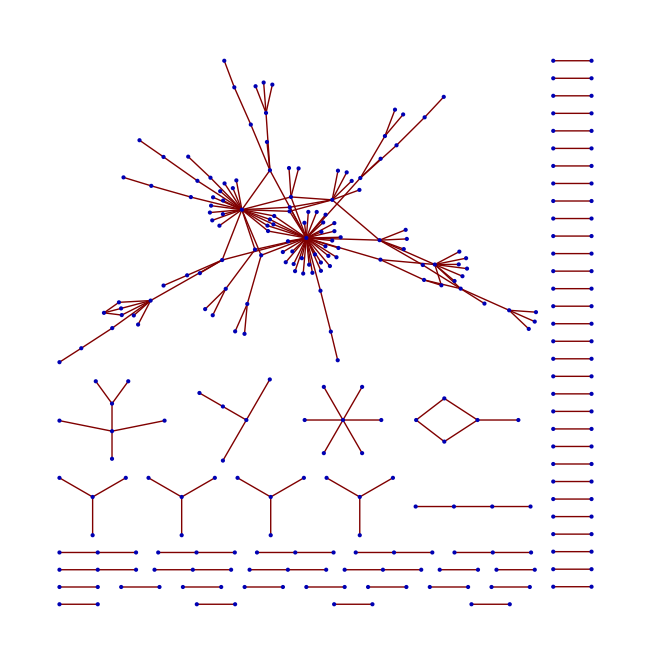

```mathematica
GraphPlot[digraph]
```